```mathematica
FormulaGraphReverse2[allGraphs5[lambdaKey,"colofourgenerator"]]//VertexList
```

prefix g

{g13x24x5,g13x25x4,g14x25x3,g14x2x35,g1x24x35,g1x2x3x4x5,g13x2x4x5,g14x2x3x5,g1x24x3x5,g1x25x3x4,g1x2x35x4}

```mathematica
FormatCoeff[c_]:=Framed[If[c<0,Style[c,Red,Bold],Style[c,Darker[Green],Italic]], Background->LightYellow]
```

```mathematica
Clear[GenGraph]
```

```mathematica
GenGraph[k_Integer, base_String:"G"]:=ShowGraph5Least[k]->GenGraph[allGraphs5[k,"colofourgenerator"],base]
```

```mathematica
GenGraph[form_, base_String:"G"]:=With[{g=FormulaGraphReverse2[form]},
Graph[g,VertexLabels->Map[#->Labeled[(#/.RepGraph[base]),FormatCoeff[Coefficient[form,#]]]&,VertexList[g]],
ImageSize->400
]
]
```

```mathematica
allGraphs5[lambdaKey,"colofour"]/.RepGraph["C"]
```

-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240

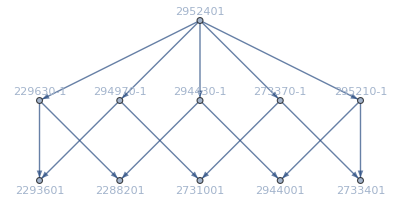
-Graphics-206653→-Graphics-

```mathematica
GenGraph[lambdaKey]
```

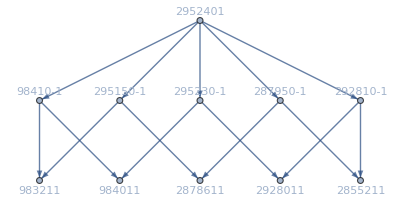
-Graphics-88595→-Graphics-

```mathematica
GenGraph[starKey]
```

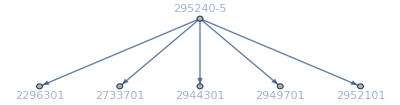

```mathematica
GenGraph[Total[Table[allGraphs5[k,"colofourgenerator"],{k,quads}]]]
```

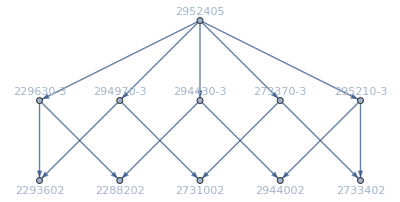

```mathematica
GenGraph[Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfas}]]]
```

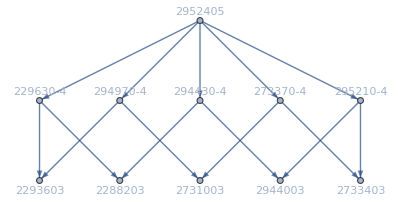

```mathematica
GenGraph[Total[Table[allGraphs5[k,"colofourgenerator"],{k,Join[alfa1s,alfas,quads ]}]]]
```

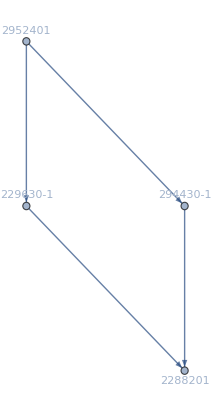
-Graphics-361660→-Graphics-

```mathematica
GenGraph[alfa1Key]
```

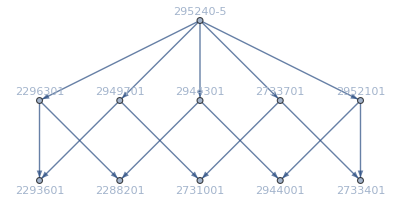

```mathematica
GenGraph[Total[Table[allGraphs5[k,"colofourgenerator"],{k,amigos}]]]
```

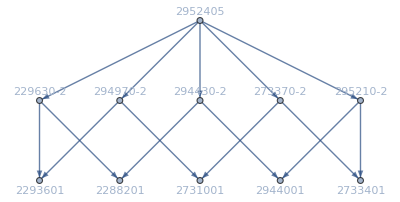

```mathematica
GenGraph[Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]]
```

```mathematica
Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]/.RepGraph["G"]
```

-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820-2 -Graphics-295210-2 -Graphics-294970-2 -Graphics-294430-2 -Graphics-273370-2 -Graphics-229630+5 -Graphics-295240

```mathematica
ListofVars[Table[allGraphs5[k,"colofourgenerator"],{k,alfas}]]
```

{g13x24x5,g13x25x4,g1x2x3x4x5,g13x2x4x5,g1x24x3x5,g1x25x3x4,g13x24x5,g1x24x35,g1x2x3x4x5,g13x2x4x5,g1x24x3x5,g1x2x35x4,g13x25x4,g14x25x3,g1x2x3x4x5,g13x2x4x5,g14x2x3x5,g1x25x3x4,g14x25x3,g14x2x35,g1x2x3x4x5,g14x2x3x5,g1x25x3x4,g1x2x35x4,g14x2x35,g1x24x35,g1x2x3x4x5,g14x2x3x5,g1x24x3x5,g1x2x35x4}

```mathematica
xquad=Total[Table[allGraphs5[k,"colofourgenerator"],{k,quads}]]
```

g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4-5 g1x2x3x4x5

```mathematica
Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]==zzzz
```

g13x24x5+g13x25x4-2 g13x2x4x5+g14x25x3+g14x2x35-2 g14x2x3x5+g1x24x35-2 g1x24x3x5-2 g1x25x3x4-2 g1x2x35x4+5 g1x2x3x4x5==zzzz

```mathematica
ListofVars[g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4]
```

{g13x2x4x5,g14x2x3x5,g1x24x3x5,g1x25x3x4,g1x2x35x4}

```mathematica
Eliminate[Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]==zzzz,ListofVars[g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4]]
```

True

```mathematica
Eliminate[g1x2x3x4x5==0&&xquad==g13x2x4x5+g14x2x3x5+g1x24x3x5+g1x25x3x4+g1x2x35x4&&Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]==zzzz,{g13x2x4x5,g14x2x3x5,g1x24x3x5,g1x25x3x4,g1x2x35x4}]
```

g1x2x3x4x5==0

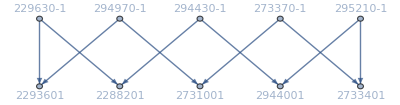

```mathematica
GenGraph[Total[Table[allGraphs5[k,"colofourgenerator"],{k,Join[alfa1s,quads]}]]]
```

```mathematica
allGraphs5[lambdaKey,"colofour"]/.RepGraph["C"]
```

-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080+-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270+-Graphics-295240

```mathematica
Total[Table[allGraphs5[k,"colofour"],{k,alfa1s}]]/.RepGraph["C"]
```

-Graphics-361660+-Graphics-361120+-Graphics-317380+-Graphics-317140+-Graphics-296080

```mathematica
Total[Table[allGraphs5[k,"colofour"],{k,quads}]]/.RepGraph["C"]
```

-Graphics-360850+-Graphics-317110+-Graphics-296050+-Graphics-295510+-Graphics-295270

```mathematica
GenGraph[lambdaKey]
```

-Graphics-206653→-Graphics-

```mathematica
Table[allGraphs5[k,"graph"],{k,alfa1s}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GenGraph[Total[Table[allGraphs5[k,"colofourgenerator"],{k,alfa1s}]]]
```

-Graphics-

```mathematica
Table[allGraphs5[k,"graph"],{k,alfas}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

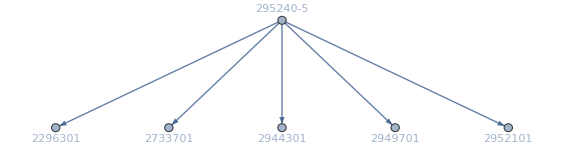

```mathematica
GenGraph[Total[Table[allGraphs5[k,"colofourgenerator"],{k,quads}]]]
```

```mathematica
Head[g13x24x5+g13x25x4-g13x2x4x5+g14x25x3+g14x2x35-g14x2x3x5+g1x24x35-g1x24x3x5-g1x25x3x4-g1x2x35x4+g1x2x3x4x5]
```

Plus

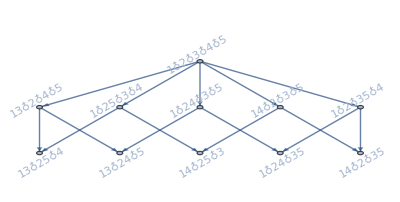

```mathematica
FormulaGraphReverse2[Total[Table[allGraphs5[lambdaKey,"colofourgenerator"],{k,alfa1s}]]]
```